# Lecture 6 - Introduction to Electricity

### A Puzzle...

We are all familiar with visualizing an integral as the area under a curve. For example, ∫_a^b f[x]ⅆx equals the sum of the areas of the rectangles of width Δ,x shown below in limit as Δ,x→0.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Furthermore, we all know the relation

∫_b^a f[x]ⅆx=-∫_a^b f[x]ⅆx

How can you visualize ∫_b^a f[x]ⅆx and determine that it is negative?

Solution
When a<b, the integral ∫_a^b f[x]ⅆx equals

∫_a^b f[x]ⅆx=lim_(N→∞) ∑_(j=0)^(N-1) f[a+j Δ,x]Δ,x

where Δ,x=(b-a)/N in the summation is the analog of ⅆx in the integral. Thus, if we flip the integration bounds,

∫_b^a f[x]ⅆx=lim_(N→∞) ∑_(j=0)^(N-1) f[a+j Δ,x̃]Δ,x̃

where Δ,x̃=(a-b)/N<0. Therefore, the ⅆx in ∫_b^a f[x]ⅆx is negative (because of the bounds), so that we are integrating a negative amount over the region of integration, yielding a negative result. □

### Electrodynamics

We now will change subjects completely and break into the world of electricity. But the real punch-line of this course will occur when we merge the concept of electricity together with special relativity to see how magnetism naturally emerges. Get pumped!

After this course, you will be able to:

Learn to love the uses of symmetry in electrostatics problems

Analyze the roles of batteries, resistors, and capacitors in circuits

Distinguish whether phenomena are primarily caused by mechanical or electrical means

Summarize the connection between electrical forces, special relativity, and magnetism

#### Coulomb Force

The Principle of Superposition states that the interaction between any two charges is completely unaffected by the presence of other charges.

Consider two point charges q_1 and q_2 separated by a direction vector (r⃗)_12 from charge 2 to charge 1. In other words, if q_1 lies at (x_1,y_1,z_1) and q_2 lies at (x_2,y_2,z_2) then (r⃗)_12=⟨x_1-x_2,y_1-y_2,z_1-z_2⟩.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

The Coulomb force from charge 2 onto charge 1 equals

(F⃗)_12≡(k q_1 q_2)/r_12^2(r̂)_12

where (r̂)_12=((r⃗)_12)/(|(r⃗)_12|), r_12=|(r⃗)_12|, and the Coulomb constant k equals

k≡1/(4π ϵ_0)≡9×10^9(N·m^2)/C^2

#### Complementary Section: Work

Let us calculate the energy required to bring in two charges from infinitely far away to a distance r_12. Fix the charge q_1 at the origin and let q_2 come radially in from ∞. The force that we have to apply on the system when the two charges are a distance r away equals (F⃗)_applied=-k(q_1 q_2)/r^2 r̂. Therefore, the total work equals

W=∫(applied force)·(displacement vector)
=∫_∞^r_12 (-(k q_1 q_2)/r^2)ⅆr
=(k q_1 q_2)/r_12

In case you are confused by the bounds on the second integral, notice that we are taking the line integral along the path l⃗=r r̂ from r=∞ to r=r_12. Therefore, the displacement vector is given by ⅆ l⃗=ⅆr r̂ so that (applied force)·(displacement vector)=(-(k q_1 q_2)/r^2 r̂)·(ⅆr r̂)=-(k q_1 q_2)/r^2ⅆr. Had we wanted to find the work necessary to start the charges a distance r_12 apart and take them out to ∞, it would have equaled W̃=∫_r_12^∞ (-(k q_1 q_2)/r^2)ⅆr=-W.

We can visualize in our mind by noting that -(k q_1 q_2)/r^2 is the force that we apply (the negative sign comes the fact that it points radially inward) and this is multiplied by the negative quantity ⅆr (negative because the integral ranges from ∞ to r_12, so an infinitesimal step points radially inward, which is negative (this is the reason why ∫_a^b f[x]ⅆx=-∫_b^a f[x]ⅆx)).

If we now bring in another charge q_3 and move it to a point P_3 that is r_13 from charge 1 and r_23 from charge 2, the work required equals

W_3=-∫_∞^P_3 (F⃗)_3·ⅆ s⃗
=-∫_∞^P_3 ((F⃗)_31+(F⃗)_32)·ⅆ s⃗
=-∫_∞^P_3 (F⃗)_31·ⅆ s⃗-∫_∞^P_3 (F⃗)_32·ⅆ s⃗

That is, the work required to bring q_3 to P_3 is the sum of the work needed when q_1 is present alone and that needed when q_2 is present alone

W_3=(k q_1 q_3)/r_13+(k q_2 q_3)/r_23

Therefore, the total work U to assemble the three charges equals

U=(k q_1 q_2)/r_12+(k q_1 q_3)/r_13+(k q_2 q_3)/r_23

which is the sum of pairwise potential energies of the particles.

### Problems

#### Balancing the Weight

Example
On the utterly unrealistic assumption that there are no other charged particles in the vicinity, at what distance below a proton would the upward force on an electron equal the electron’s weight? The mass of an electron is about 9 10^-31 kg.

Solution
The proton and electron have charges e=1.6 10^-19 C and -e, respectively. Assume the electron and proton are separated by a distance d. Then the electron feels an attractive force (k e^2)/d^2 up towards the proton, and an attractive force m g down towards the Earth. Recalling that k=9×10^9(N·m^2)/C^2 and g=9.8 m/s^2, these two forces are equal when (k e^2)/d^2=m g which yields d≈5meters.

So the electric force of a single proton balances the gravitational force of the entire mass of the Earth at 5 meters away (and is much stronger at closer distances). To give a sense of how ridiculously strong this is, consider the same problem if we neutralized the charges on the electron and proton, and asked how small d must be so that the gravitational force of the neutralized proton balances that of the electron. Using the exact form of the gravitational force for simplicity (with E subscript denoting the Earth and p subscript denoting the neutralized proton), (G M_E m)/R_E^2=(G m_p m)/d^2 which yields d=(R_E(m_p/m_E))^(1/2)≈(6.4 10^6 m)((1.7 10^-27 kg)/(6 10^24 kg))^(1/2)≈10^-19 m, a much smaller distance than we can measure with the best microscopes. This is why people often say that the gravitational force is much weaker then the electrostatic force. □

#### Zero Force from a Triangle

Example
Two positive ions and one negative ion are fixed at the vertices of an equilateral triangle. Where can a fourth ion be placed in the plane of the triangle along the symmetry axis so that the force on it will be zero? Is there more than one such place?

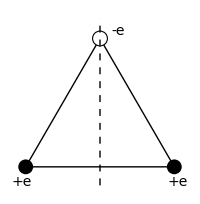

```mathematica
{a,b,c}={{-1,0},{1,0},{0,√3}};
centerPlot@Graphics[{Line[{a,b,c,a}],Disk[a,0.1],Disk[b,0.1],EdgeForm[Black],FaceForm[White],Disk[c,0.1],Dashed,Line[{{0,-0.25},{0,2}}],Text[font@"-e",c+{0.25,0.1}],Text[font@"+e",a+{-0.06,-0.2}],Text[font@"+e",b+{0.05,-0.2}]},ImageSize->200]
```

Solution
First, note that the desired point cannot be located in the interior of the triangle, because the components of the fields along the symmetry axis would all point in the same direction (toward the negative ion). Let the sides of the triangle be 2 units long. Consider a point P that lies a distance y (so y is defined to be a positive number) beyond the side containing the two positive ions, as shown below. P is a distance y+√3 from the negative ion, and (1+y^2)^(1/2) from each of the positive ions.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

If the electric field equals zero at P, then the upward field due to the negative ion must cancel the downward field due to the two positive ions. This gives

(k e^2)/(y+√3)^2=2 (k e^2)/(1+y^2)y/((1+y^2)^(1/2))

where y/((1+y^2)^(1/2)) arises from taking the vertical component of the tilted field lines due to the positive ions. This equation can be simplified to

y=((1+y^2)^(3/2))/(2(y+√3)^2)

which can be solved numerically as y=0.146

```mathematica
NSolve[y==((1+y^2)^(3/2))/(2(y+√3)^2),y,Reals]
```

{{y→0.14629}}

A second point with zero force lies somewhere beyond the negative ion. To locate it, let y now be the distance (so y is still a positive quantity) from the same origin as before (the midpoint of the side connecting the two positive ions). We obtain the same equation as above, except that +√3 is replaced with -√3. The numerical solution is now y=6.204, which corresponds to the distance that the negative ion should be placed above the triangle vertex with the negative ion.

```mathematica
NSolve[{y==((1+y^2)^(3/2))/(2(y-√3)^2),y>√3.},y,Reals]
```

{{y→6.20448}}

The existence of each of these points with zero field follows from a continuity argument. For the upper point: the electric field just above the negative ion points downward. But the field at a large distance above the setup points upward, because the triangle looks effectively like a point charge with net charge +e from afar. Therefore, by continuity there must be an intermediate point where the field makes the transition from pointing downward to pointing upward. So the force must be zero at this point. A similar continuity argument holds for the lower point.

Finally, we discuss how this problem is scale invariant, and hence why we did not need to specify the side length of the triangle. Denote the origin as the centroid of the triangle and label the three triangle charges starting from the electron and moving clockwise as 1, 2, and 3. Suppose a negative charge placed the point (r⃗)_4=(0,y) had zero net force

F⃗=(k q_4 q_1)/r_41^2(r̂)_41+(k q_4 q_2)/r_42^2(r̂)_42+(k q_4 q_3)/r_43^2(r̂)_43

Now if the triangle is scaled up to be α times larger (i.e. if all of the triangle's vertices were shifted from (r⃗)_j→α (r⃗)_j), then a negative charge placed at (0,α y) would feel zero net force because the three (r̂)_(4,j) directions in Equation (TextNumbered) would not have changed but the denominators in Equation (TextNumbered) would all be 1/α^2 times as large (and 1/α^2·0=0). Therefore, the side length of the triangle sets the scale for the problem, so our answer can be thought of as finding the two points of zero net force in this unit system. □

#### Charges on a Circular Track

Example
Suppose three positively charged particles are constrained to move on a fixed circular track. If the charges were all equal, an equilibrium arrangement would obviously be a symmetrical one with the particles spaced 120° apart around the circle. Suppose that two of the charges are equal and the equilibrium arrangement is such that these two charges are 90° apart rather than 120°. What is the relative magnitude of the third charge?

Solution
Method 1: We can solve for θ by noting that the tangential force on either charge q must be zero.

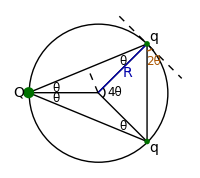

```mathematica
p1={Cos[π/4],Sin[π/4]};
p2={Cos[-π/4],Sin[-π/4]};
p3={Cos[π],Sin[π]};
p4={p1[[2]]+0.5,p1[[2]]-0.5 p1[[2]]/p1[[1]]};
p5={p1[[2]]-0.4,p1[[2]]+0.4 p1[[2]]/p1[[1]]};
centerPlot@Graphics[{Circle[],Circle[{0,0},0.1,{-π/4,π/4}],Line[{{p2,{0,0},p1},{{0,0},p3},{p1,p2,p3,p1}}],{Darker@Blue,Line[{{0,0},p1}]},{Dashed,Line[{{p5,p4},{{0,0},Mean[{p1,p3}]}}]}(*,Dashing[Tiny],Line[{{0,0},{1,0}}]*),Text[font["θ",12],{-0.6,0.06}],Text[font["θ",12],{-0.6,-0.09}],Text[font["θ",12],p1/2+{-0.0,0.10}],Text[font["θ",12],p2/2+{-0.0,-0.13}],{Darker@Orange,Circle[p1,0.1,{-π/2,-π/4}],Text[font["2θ",12],p1+{0.09,-0.25}]},Text[font["4θ",12],{0.24,0}],Text[font["q",Italic],p1+{0.1,0.1}],Text[font["q",Italic],p2+{0.1,-0.1}],Text[font["Q",Italic],p3+{-0.15,0}],{Darker@Blue,Text[font["R",Italic],p1/2+{0.07,-0.07}]},Darker@Darker@Green,PointSize[0.02],Point[{p1,p2}],PointSize[0.04],Point[p3]},ImageSize->200]
```

The tangential force on one of the q’s due to Q equals

(k Q q)/(2R Cos[θ])^2 Sin[θ]

while the tangential force from the other q equals

(k q^2)/(2R Sin[2θ])^2 Cos[2θ]

Setting these two forces equal yields the result

Q=q(Cos[θ]^2 Cos[2θ])/(Sin[θ]Sin[2θ]^2)=q Cos[2 θ]/(4 Sin[θ]^3)

For the particular case of θ=π/8 given in the problem, Q=3.154q

Method 2: Define the angle between the two charges q to be 4θ (the reason to make it 4θ will be apparent in the solution of Method 2 below). We can compute the potential energy of this more general system, then compute its minimum, and find Q such that this minimum occurs at 4θ=π/2.

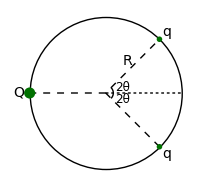

```mathematica
p1={Cos[π/4],Sin[π/4]};
p2={Cos[-π/4],Sin[-π/4]};
p3={Cos[π],Sin[π]};
centerPlot@Graphics[{Circle[],Circle[{0,0},0.1,{-π/4,π/4}],Dashed,Line[{{p2,{0,0},p1},{{0,0},p3}}],Dashing[Tiny],Line[{{0,0},{1,0}}],Text[font["2θ",12],{0.22,0.07}],Text[font["2θ",12],{0.22,-0.09}],Text[font["q",Italic],p1+{0.1,0.1}],Text[font["q",Italic],p2+{0.1,-0.1}],Text[font["Q",Italic],p3+{-0.15,0}],Text[font["R",Italic],p1/2+{-0.07,0.07}],Darker@Darker@Green,PointSize[0.02],Point[{p1,p2}],PointSize[0.04],Point[p3]},ImageSize->200]
```

The potential energy of this system equals the sum U=∑_(q≠k) (k q_j q_k)/(r_(j,k)) over all pairs, which equals

U=(k q^2)/(2R Sin[2θ])+(2k q Q)/(R ((1+Cos[2θ])^2+Sin[θ]^2)^(1/2))

The procedure is now straightforward (although algebraically messy). By symmetry, the system must take the above consideration; its only degree of freedom will be choosing the value of θ. Therefore, the system will be in equilibrium when the energy is minimized with respect to θ.

Taking the derivative (and simplifying)

ⅆU/ⅆθ=1/R(-q/(Tan[2θ]Sin[2θ])+(Q Tan[θ])/Cos[θ])

Setting this equal to zero (and simplifying) yields the same answer found above,

Q=q Cos[θ]/(Tan[2θ]Tan[θ]Sin[2θ])=q Cos[2 θ]/(4 Sin[θ]^3)

The following confirms the answer using Mathematica

```mathematica
res=First@FullSimplify[Solve[D[q/(2R Sin[2θ])+2 Q/(R √((1+Cos[2θ])^2+Sin[2θ]^2)),θ]==0,Q],0<θ<π/2]
res/.θ->π/8.
```

{Q→1/4 q Cos[2 θ] Csc[θ]^3}

{Q→3.15432 q}

Let’s check some interesting limits: 
1. When the three charges are equally spaced (θ=30°) then Q=q, as expected.
2. If the q’s are diametrically opposite (θ=45°) then Q=0, as expected.
3. If θ→0, then Q≈q/(4 θ^3). Two of these powers of θ come from the 1/r^2 in Coulomb’s law from the q’s mutual repulsion, and one comes from the act of taking the tangential component of Q’s electric force. □

### Integration

#### The Mathematics of 1D Integration

From this point on, we will begin to consider spherical configurations of charge distributions. As preparation for some of the difficult integration that we are going to perform in this class, let’s do two simple exercises. These problems (as well as 2D and 3D integration) are done in the Math Bootcamp: Volume Elements posted on my website!

Prove that the length of the horizontal line between (x,y) and (x+a,y) equals a

Breaking this horizontal line into small chunks of length ⅆx, the total length of this horizontal line equals

∫_x^(x+a) ⅆx=(x+a)-x=a

Prove that the perimeter of a circle of radius R is 2π R

In polar coordinates, the arc of a circle between θ and θ+ⅆθ has length Rⅆθ. Since the circle spans θ∈[0,2π], the perimeter of the circle equals

∫_0^(2π) Rⅆθ=2π R

#### Force from a Semicircle

Example
A thin rod bent into a semicircle of radius R has a charge Q distributed uniformly over its length. What is the electric force on a charge q at the center of the semicircle?

Solution
We use polar coordinates and align the semicircle to span θ∈[0,π]. The charge density of the semicircle equals λ=Q/(π R) and a small portion of the semicircle between θ and θ+ⅆθ has charge λ R ⅆθ. Therefore, a charge q at the center would feel a force ⅆ F_θ=(k q (λ R ⅆθ))/R^2 at the center.

```mathematica
centerPlot@-Graphics-
```

-Graphics-

By the symmetry of the semicircle, the total force on charge q must point in the -y direction (indeed, the x-component of the ⅆ F_θ shown in the figure above is canceled by that of the ⅆ F_(π-θ) component). The magnitude of the y-component equals ⅆ F_θSin[θ]. Therefore, the total force on charge q equals F⃗=(-ŷ)∫ⅆ F_θSin[θ] which implies

F⃗=(-ŷ)∫_0^π (k q λ R ⅆθ)/R^2 Sin[θ]=-(2k q λ)/R ŷ=-(2k q Q)/(π R^2)ŷ

The electric field at the center of the semicircle equals this force divided by the charge q,

E⃗=-(2k Q)/(π R^2)ŷ

#### The Mathematics of 2D Integration

Let’s step it up a notch and consider 2D integrals.

Prove that the area of the rectangle between (x,y), (x+a,y), (x,y+b), and (x+a,y+b) equals a b

The area element in 2D Cartesian coordinates is ⅆxⅆy, and hence the total area equals

∫_y^(y+b) ∫_x^(x+a) ⅆxⅆy=a b

Prove that the area of a circle of radius R is π R^2

The area element in 2D polar coordinates is r ⅆrⅆθ, and hence the area of the circle equals

∫_0^(2π) ∫_0^R rⅆrⅆθ=∫_0^(2π) 1/2 R^2 ⅆθ=π R^2

#### Force from a Disk

Example
A circular sheet of radius R has a charge Q distributed uniformly over its area. The sheet lies in the x-z plane as shown below. What is the electric force on a charge q placed at a point (0,y,0) along the axis of symmetry?

```mathematica
centerPlot@-Graphics-
```

-Graphics-

Solution
Define the surface charge density σ=Q/(π R^2). In addition, define the polar coordinates (r,θ) where r represents the distance from the origin and θ represents the angle above the x-axis. By symmetry, the net force on q must point along the ŷ-direction (the electric force from an infinitesimal element at (r,θ) added to the force from the element at (r,θ+π) will yield a force pointing in the ŷ-direction). Therefore, the we only need to compute the y-component of the electric force from every part of the sheet and add them together. To show that there are multiple ways to perform such integration, we proceed with two methods.

Method 1: Integrate using the polar coordinate area element
The y-component of the force on q arising from the area element rⅆrⅆθ at (r,θ) is given by (k q (σ rⅆrⅆθ))/(y^2+r^2)y/((y^2+r^2)^(1/2)) where the last term pulls out the y-component of the force. Therefore, the total force on q equals

F⃗=ŷ∫_0^(2π) ∫_0^R (k q (σ rⅆrⅆθ))/(y^2+r^2)y/((y^2+r^2)^(1/2))
=ŷ∫_0^(2π) (-(k q σ yⅆθ)/((y^2+r^2)^(1/2)))_(r=0)^(r=R)
=ŷ∫_0^(2π) (k q σ-(k q σ y)/((y^2+R^2)^(1/2)))ⅆθ
=2π k q σ(1-y/((y^2+R^2)^(1/2)))ŷ
=(2k q Q)/R^2(1-y/((y^2+R^2)^(1/2)))ŷ

The plot below shows the term in parenthesis for R=1, and the result should appear rather puzzling. While it does drop off with larger y (as expected), the force does not go to zero at y=0 (as it must be symmetry)!

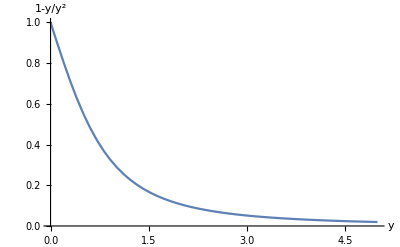

```mathematica
centerPlot@Plot[1-y/((y^2+1)^(1/2)),{y,0,5},PlotRange->All,AxesLabel->font/@{"y","1-y/y^2"}]
```

In addition, we know that the force for negative y values must be pointed in the -ŷ direction, so the net force for all y must look something like this

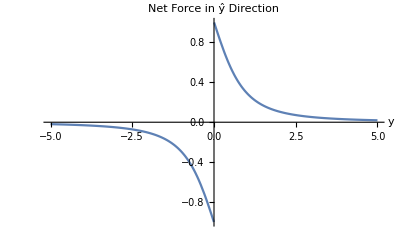

```mathematica
centerPlot@Plot[Piecewise[{{1-y/((y^2+1)^(1/2)),y>0},{-1-y/((y^2+1)^(1/2)),y<0}}],{y,-5,5},PlotRange->All,AxesLabel->font/@{"y","Net Force in ŷ Direction"}]
```

By this point, you should be very surprised to see a discontinuity! Indeed, in the next lecture we will see that sheets of charge always result in a discontinuous force when you cross the sheet. For now, let’s conduct a sanity check by doing the integration in a slightly different manner.

Method 2: Integrate along rings
Rather than integrating over an individual area element r ⅆrⅆθ in polar coordinates, let’s integrate over rings (like the shaded area in the diagram above). Although exactly identical to Method 1, these types of tricks enable us to double check ourselves, and occasionally pay off with greatly simplified calculations. A ring of radius r and width ⅆr has area 2π rⅆr and therefore charge 2π r σⅆr. The force from such a ring must point in the ŷ-direction by symmetry, and its magnitude will be (k q 2π r σⅆr)/(y^2+r^2)y/((y^2+r^2)^(1/2)) where the second term pulls out the y-component of the force, as we found in Method 1. Note that we have essentially carried out the θ-integral in Equation (TextNumbered). The net force from the circular sheet will be

F⃗=ŷ∫_0^R (k q 2π r σⅆr)/(y^2+r^2)y/((y^2+r^2)^(1/2))
=ŷ (-(k q 2π σ y)/((y^2+r^2)^(1/2)))_(r=0)^(r=R)
=ŷ (k q 2π σ-(k q 2π σ y)/((y^2+R^2)^(1/2)))
=(2k q Q)/R^2(1-y/((y^2+R^2)^(1/2)))ŷ

as we found before. □

#### The Mathematics of 3D Integration

Finally, we reach our last level of dimensions - our three dimensional world. Everything in electricity will be assumed to be three dimensional, even though we will often only consider one or two dimensions when symmetry permits.

Prove that the area of the rectangular prism between (x,y,z), (x+a,y,z), (x,y+b,z), (x,y,z+c), (x+a,y+b,z), (x+a,y,z+c), (x,y+b,z+c), and (x+a,y+b,z+c) equals a b c

The volume element in 3D Cartesian coordinates is ⅆxⅆyⅆz, and hence the total area equals

∫_z^(z+c) ∫_y^(y+b) ∫_x^(x+a) ⅆxⅆyⅆz=a b c

Prove that the volume of a sphere of radius R is 4/3 π R^3

The volume element in 3D polar coordinates is r^2 Sin[θ] ⅆrⅆθⅆϕ, and hence the volume of the sphere equals

∫_0^(2π) ∫_0^π ∫_0^R r^2 Sin[θ]ⅆrⅆθⅆϕ=∫_0^π 2π (1/3 R^3)Sin[θ]ⅆθ=4/3 π R^3

With this mathematical machinery, we are all set to tackle many interesting in electrodynamics!

### Advanced Section: Electric Energy vs Thermal Energy

In statistical mechanics, you will learn that the microscopic world behaves completely differently from our macroscopic world. For example:

Proteins float: Gravity still exists, but there is a countering force that makes it negligible

Nothing is stationary: All molecules are constantly wiggling around, a process known as Brownian motion

Electric shielding: DNA is extremely negatively charged, and a cell is full of ions, but these ions are not drawn to the DNA

Here, we sketch an outline of these points. Before getting into it, suppose that you find a $10 bill on the ground. You will feel pretty happy, but it will just be a short burst of happiness, and you will not be overly surprised to have found the money. Anything less than $10 is chump change - if your friend asks you for two dollars, you will not hesitate to give it to them, and you will likely not hold them accountable for that money. On the other hand, finding a $100 is very surprising, and you will almost certainly hesitate before lending you friend this amount. In this setup, $10 marks the scale of a typical meaningful monetary transaction - anything smaller is irrelevant and anything larger is important.

In statistical mechanics, the fundamental energy scale is defined to be 1 k_B T where k_B=1.38×10^-23(kg·m^2)/(s^2·K) and T is the temperature. At room temperature, 1 k_B T=4.14×10^-21J. As in the above example, this is the energy allowance that every single process in the universe has at a given temperature. Any process that takes less energy than this happens on a regular basis; any process that takes significantly more energy will be rare.

With this in mind, let us think about the three effects stated above:

A protein of mass m will be expected to float up to a height h defined by m g h=k_B T

A mass m is expected to have an average velocity given by 1/2 m⟨v^2⟩=k_B T

A proton will not feel the effects of an electron if it is further away than a distance d defined by

(k e^2)/d=k_B T

Substituting in the numbers yields d=50 10^-9 m=50nm. You should be shocked! This implies that random thermal fluctuations make the electric force negligible beyond 50 nanometers. This is insane, since we have just learned that the electric field is so much stronger than the gravitational force. But temperature has a power all of its own.

## Mathematica Initialization

```mathematica
Clear[font]
font[text_,size_Integer:14,opts___]:=(Style[text,size,FontFamily->"Times",opts])
```

```mathematica
RawBoxes@CounterBox["TextNumbered","eq1"]
```

TextNumbered